## Physical constants

```mathematica
me=9.11*10^(-31)
```

9.11×10^-31

```mathematica
mn=1.67*10^(-27)
```

1.67×10^-27

```mathematica
c=299792458
```

299792458

```mathematica
pi=3.14152965
```

3.14153

```mathematica
hbar=1.055*10^(-34)
```

1.055×10^-34

In epsl0, change between m_n and m_e to calculate polytrope either for neutron star or white dwarf.

```mathematica
epsl0=mn^4*c^5/(pi^2*hbar^3)
```

1.62529×10^36

## Integrating to find energy density

Here,  x = k_f / (m_e*c).

```mathematica
Y=Integrate[(u^2+1)^(1/2)*u^2,{u,0,x}]
```

ConditionalExpression[1/8 (x √(1+x^2) (1+2 x^2)-ArcSinh[x]),Re[x]≠0||-1<Im[x]<0||0<Im[x]<1]

```mathematica
Energy=Y*epsl0+mn*mn^3*c^5*2*x^3/(3*pi^2*hbar^3)
```

ConditionalExpression[1.08352×10^36 x^3+6.77202×10^34 (x √(1+x^2) (1+2 x^2)-ArcSinh[x]),Re[x]≠0||-1<Im[x]<0||0<Im[x]<1]

The second term is the rest mass energy of the nucleons. For derivation see the written note pp.4.

```mathematica
Plot[Energy,{x,0,2}]
```

-Graphics-

Plot of m_e*c versus the energy density, in the range of 0 to 2 electron mass (times c)

## Finding pressure

```mathematica
Y2=Integrate[(u^2+1)^(-1/2)*u^4/3,{u,0,x}]
```

ConditionalExpression[1/24 (x √(1+x^2) (-3+2 x^2)+3 ArcSinh[x]),Re[x]≠0||-1<Im[x]<0||0<Im[x]<1]

```mathematica
Pressure=Y2*epsl0
```

ConditionalExpression[2.25734×10^34 (x √(1+x^2) (-3+2 x^2)+3 ArcSinh[x]),Re[x]≠0||-1<Im[x]<0||0<Im[x]<1]

```mathematica
Plot[Pressure,{x,0,2}]
```

-Graphics-

Plot of m_e*c  versus the pressure, in the range of 0 to 2 electron mass (times c)

## Finding the fit for energy density vs pressure

```mathematica
ParametricPlot[{Pressure,Energy},{x,0,2},AspectRatio-> 1,ImageSize->Large]
```

-Graphics-

Plot of energy density versus the pressure, in the range of the parameter m_e (mass of electron) between 0 and 2. The units for both of them are in J/m^3.

Here the data is created between the range {x, start, end, step}. Giving ‘start’=0 results in error, so small number is used. As ‘end’ is changed, the result of the fit also changes, which is problematic.

```mathematica
fitdata=Table[{Pressure/epsl0,Energy/epsl0},{x,0.0001,1,0.0001}];
```

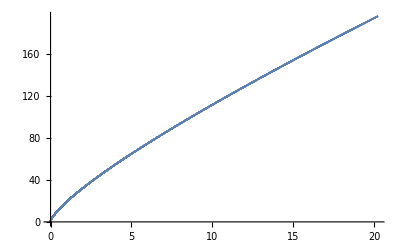

```mathematica
ListPlot[fitdata]
```

For neutron star, use the 1/gamma of 3/5 and 1, for white dwarf 3/5 and 3/4 (E=p^(1/gamma)).

```mathematica
Energyfit=Fit[fitdata,{x^(3/5),x^(1)},x]
```

7.68668 x^(3/5)+8.10528 x

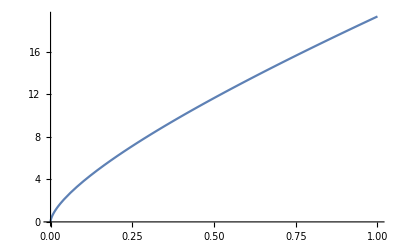

```mathematica
Plot[Energyfit,{x,0,1}]
```